# 30 minute geography computational essay

Peter Cullen Burbery

Abstract

## Section

I want to know my latitude and longitude.

XXXX:

```mathematica
Here
```

GeoPosition[{38.41,-82.44}]

I want to find my antipode, the point directly opposite me on Earth.

```mathematica
GeoAntipode[Here]
```

GeoPosition[{-38.41,97.56}]

Find the sunrise.

```mathematica
Sunrise[Here]
```

Minute: Mon 12 Sep 2022 07:09GMT-4

```mathematica
Sunset[Here]
```

Minute: Mon 12 Sep 2022 19:43GMT-4

Find the length of the day:

```mathematica
Sunset[Here]-Sunrise[Here]
```

754 min

Convert to hours, minutes, seconds, nanoseconds, and zeptoseconds:

```mathematica
UnitConvert[Sunset[Here]-Sunrise[Here],MixedUnit[{"Hours","Minutes","Seconds","Nanoseconds","Zeptoseconds"}]]
```

12 34

Convert to SI base units:

```mathematica
UnitConvert[Quantity[MixedMagnitude[{12,34,0,0,0}],MixedUnit[{"Hours","Minutes","Seconds","Nanoseconds","Zeptoseconds"}]]]
```

45240 s

Draw a map:

```mathematica
GeoGraphics[Arrow@GeoPath[{Here,Entity["City",{"Paris","IleDeFrance","France"}]}],GeoBackground->"ReliefMap",ImageSize->Full]
```

-Graphics-

Find the distance to the Empire State Building:

```mathematica
GeoDistance[Here,Entity["Building","EmpireStateBuilding::h583b"]]
```

770.97 km

Find the azimuth direction:

```mathematica
GeoDirection[Here,Entity["Building","EmpireStateBuilding::h583b"]]
```

67.6687 °

Draw my location on a map:

```mathematica
GeoGraphics[GeoDisk[Here,Quantity[5000, "Kilometers"]]]
```

-Graphics-

Find directions to New York City:

```mathematica
NYCTRAVELDIRECTIONS=TravelDirections[{Here,Entity["City",{"NewYork","NewYork","UnitedStates"}]}]
```

TravelDirectionsData[…]

Find the duration:

```mathematica
NYCTRAVELDIRECTIONS["TravelTime"]
```

10 h

Draw the path on a map:

```mathematica
GeoGraphics[GeoPath[NYCTRAVELDIRECTIONS],ImageSize->Full,GeoBackground->"VectorBusiness"]
```

-Graphics-

Find the distance:

```mathematica
TravelDistance[{Here,Entity["City",{"NewYork","NewYork","UnitedStates"}]}]
```

944.06 km

Convert dms to decimal:

```mathematica
FromDMS[{12,37,43}]
```

45463/3600

```mathematica
FromDMS[{12,37,43}]//N
```

12.6286

```mathematica
Rationalize[FromDMS[{12,37,43}]//N]
```

45463/3600

```mathematica
FromDMS["36deg 17min 19sec E 37deg 23 min 29 sec N"]
```

{134609/3600,130639/3600}

```mathematica
FromDMS["36deg 17min 19sec E 37deg 23 min 29 sec N"]//N
```

{37.3914,36.2886}

```mathematica
DMSString[FromDMS["36deg 17min 19sec E 37deg 23 min 29 sec N"]//N]
```

37°23'29.000"N 36°17'19.000"E

```mathematica
DMSList/@FromDMS["36deg 17min 19sec E 37deg 23 min 29 sec N"]//N
```

{{37.,23.,29.},{36.,17.,19.}}

```mathematica
Latitude[Here]
```

38.41 °

```mathematica
Longitude[Here]
```

-82.44 °

```mathematica
LatitudeLongitude[Here]
```

{38.41 °,-82.44 °}

```mathematica
GeoPosition[FromDMS["36deg 17min 19sec E 37deg 23 min 29 sec N"]//N]
```

GeoPosition[{37.3914,36.2886}]

```mathematica
GeoPositionXYZ[GeoPosition[FromDMS["36deg 17min 19sec E 37deg 23 min 29 sec N"]//N]]
```

GeoPositionXYZ[{4.08966×10^6,3.0029×10^6,3.85199×10^6}]

```mathematica
GeoPositionENU[,GeoPosition[FromDMS["36deg 17min 19sec E 37deg 23 min 29 sec N"]//N]]
```

GeoPositionENU[{-4.53908×10^6,4.32912×10^6,-5.18761×10^6},GeoPosition[{37.3914,36.2886}]]

```mathematica
pos=GeoPosition[CountryData["UnitedStates","Coordinates"]];
```

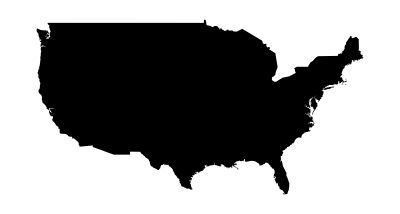

```mathematica
Graphics[Polygon[GeoGridPosition[pos,"Mercator"][[1]]]]
```

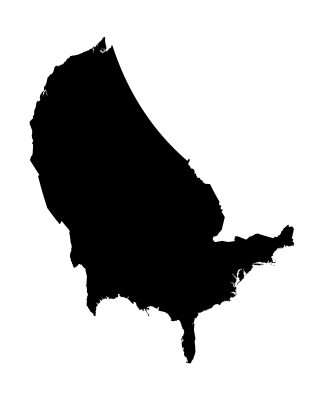

```mathematica
Graphics[Polygon[GeoGridPosition[pos,{"Cassini","Centering"->{-20,-50}}][[1]]]]
```

```mathematica
GeoGraphics[Polygon[Entity["Country","UnitedStates"]],GeoProjection->{"Cassini","Centering"->{-20,-50}},GeoBackground->"VectorBusiness"]
```

-Graphics-

Add a polygon:

```mathematica
GeoGraphics[{Polygon[Entity["Country","UnitedStates"]],GeoDisk[Here,Quantity[500, "Kilometers"]]},GeoProjection->{"Cassini","Centering"->{-20,-50}},GeoBackground->"VectorBusiness"]
```

-Graphics-

```mathematica
GeoGridPosition[GeoPosition[{37.,-19.,0}],{"Bonne","Centering"->{-35,-100}}]
```

GeoGridPosition[{0.980327,1.12387,0},{Bonne,Centering→{-35,-100}}]

```mathematica
GeoGridPosition[GeoPosition[{37.,-19.,0}],{"Albers","Centering"->{-35,-100},"StandardParallels"->{23,43}}]
```

GeoGridPosition[{1.01024,1.49094,0},{Albers,Centering→{-35,-100},StandardParallels→{23,43}}]

```mathematica
GeoGridPosition[GeoPosition[{37.,-19.,0}],{"Bonne","Centering"->{-35,-100},"StandardParallels"->{23,43}}]
```

GeoGridPosition[{1.07601,0.940504,0},{Bonne,Centering→{-35,-100},StandardParallels→{23,43}}]

```mathematica
GeoGraphics[{Polygon[Entity["Country","UnitedStates"]],GeoDisk[Here,Quantity[500, "Kilometers"]]},GeoProjection->{"Bonne","Centering"->{-20,-50}},GeoBackground->"VectorBusiness"]
```

-Graphics-

```mathematica
GeoGraphics[{Polygon[Entity["Country","UnitedStates"]],GeoDisk[Here,Quantity[500, "Kilometers"]]},GeoProjection->{"Bonne","Centering"->{-20,-50},"StandardParallels"->{13,37}},GeoBackground->"VectorBusiness"]
```

-Graphics-

```mathematica
GeoGraphics[{Polygon[Entity["Country","UnitedStates"]],GeoDisk[Here,Quantity[500, "Kilometers"]]},GeoProjection->{"Albers"},GeoBackground->"VectorBusiness"]
```

-Graphics-

```mathematica
GeoGraphics[{Polygon[Entity["Country","UnitedStates"]],GeoDisk[Here,Quantity[500, "Kilometers"]]},GeoProjection->{"Albers","Centering"->{-20,-50}},GeoBackground->"VectorBusiness"]
```

-Graphics-

```mathematica
GeoGraphics[{Polygon[Entity["Country","UnitedStates"]],GeoDisk[Here,Quantity[500, "Kilometers"]]},GeoProjection->{"Albers","Centering"->{-20,-50},"StandardParallels"->{13,37}},GeoBackground->"VectorBusiness"]
```

-Graphics-

```mathematica
RandomGeoPosition[]
```

GeoPosition[{-40.8008,108.068}]

```mathematica
RandomGeoPosition[100]
```

GeoPosition[…]

## Spatial Statistics

```mathematica
WESTVIRGINIADATA=RandomGeoPosition[Polygon[],100000]
```

GeoPosition[…]

```mathematica
SpatialMedian[WESTVIRGINIADATA]
```

GeoPosition[{38.6218,-80.6881}]

```mathematica
μ=PointDensity[WESTVIRGINIADATA]
```

7                                       -6            -6           -6            -7            -6                        -7            -6            -6
PointDensityFunction[{Delaunay, Geo}, {InterpolatingFunction[{{-0.0276693, 0.0391293}, {-0.0216881, 0.0380761}}, <>], RegionMemberFunction[MeshRegion[<2>, <2>], <>], 0.}, {0.00063349, 5.83971 10 }, <|Weights -> {0.00037116, 3.66634 10  , 3.48797 10  , 8.2407 10  , 2.83482 10  , 3.60023 10  , <<100023>>, 5.14188 10  , 1.38412 10  , 2.05265 10  }, <<4>>|>, {100000, 2}]

```mathematica
GeoVector[Here->{,Quantity[50, "AngularDegrees"]}]
```

GeoVector[GeoPosition[{38.41,-82.44}]→{1000 km,50 °}]

```mathematica
GeoVectorXYZ[GeoVector[Here->{,Quantity[50, "AngularDegrees"]}]]
```

GeoVectorXYZ[GeoPosition[{38.41,-82.44}]→{706.845 km,496.667 km,503.679 km}]

```mathematica
GeoVectorENU[GeoVector[Here->{,Quantity[50, "AngularDegrees"]}]]
```

GeoVectorENU[GeoPosition[{38.41,-82.44}]→{1000 Cos[(2 π)/9] km,1000 Sin[(2 π)/9] km}]